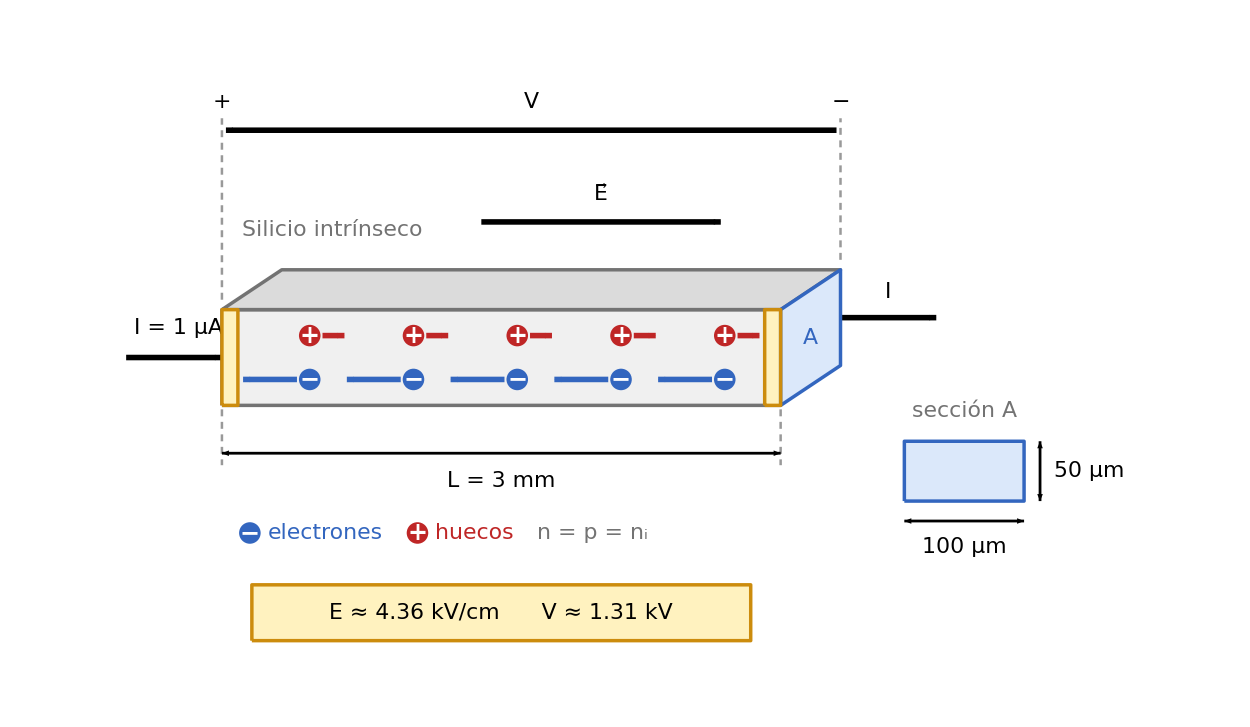

```mathematica
diagramaBarraSi = Module[
  {fs, mostrarValores, cAzul, cAzulB, cRojo, cGris, cOro, cOroB,
   e, ni, mun, mup, Icor, Ar, Lc, sig, Ecam, Vten, fmt,
   x0, x1, hh, pd, qd, xs, ins, insI, flecha, caja, cara, carga, cotaH, cotaV},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;                 (* tamaño de fuente único para todo el gráfico *)
  mostrarValores = True;   (* False oculta el recuadro con E y V *)
  cAzul = RGBColor[0.86, 0.91, 0.98];  cAzulB = RGBColor[0.20, 0.40, 0.75];
  cRojo = RGBColor[0.75, 0.15, 0.15];  cGris  = GrayLevel[0.45];
  cOro  = RGBColor[1.0, 0.95, 0.75];   cOroB  = RGBColor[0.80, 0.55, 0.05];

  (* ---------- Datos del problema (cm, V, A, s) ---------- *)
  e = 1.6*10^-19;  ni = 1.45*10^10;  mun = 1500;  mup = 475;
  Icor = 10^-6;  Ar = (50*10^-4) (100*10^-4);  Lc = 0.3;
  sig  = e ni (mun + mup);
  Ecam = (Icor/Ar)/sig;    (* V/cm *)
  Vten = Ecam Lc;          (* V *)
  fmt[x_] := ToString[NumberForm[x, {3, 2}]];

  (* ---------- Geometría (esquemática, no a escala) ---------- *)
  {x0, x1, hh} = {2.5, 16.5, 2.4};   (* extremos de la barra y altura *)
  {pd, qd} = {1.5, 1.0};             (* desplazamiento de la proyección oblicua *)
  xs = Table[x0 + 2.2 + 2.6 k, {k, 0, 4}];   (* posiciones de los portadores *)

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  insI[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Left, Center}];
  flecha[p1_, p2_, col_, s_: 0.022] :=
    {col, AbsoluteThickness[4], Arrowheads[s], Arrow[{p1, p2}]};
  caja[{xc_, yc_}, {w_, h_}, relleno_, borde_] :=
    {EdgeForm[{AbsoluteThickness[2.5], borde}], relleno,
     Rectangle[{xc - w/2, yc - h/2}, {xc + w/2, yc + h/2}, RoundingRadius -> 0.15]};
  cara[pts_, relleno_, borde_] :=
    {relleno, EdgeForm[{AbsoluteThickness[2.5], borde}], Polygon[pts]};
  carga[pos_, signo_, col_] :=
    {col, Disk[pos, 0.27], Text[Style[signo, Round[1.1 fs], Bold, White], pos]};
  cotaH[xa_, xb_, y_] :=
    {Black, AbsoluteThickness[2], Arrowheads[{-0.012, 0.012}], Arrow[{{xa, y}, {xb, y}}]};
  cotaV[x_, ya_, yb_] :=
    {Black, AbsoluteThickness[2], Arrowheads[{-0.012, 0.012}], Arrow[{{x, ya}, {x, yb}}]};

  (* ---------- Diagrama ---------- *)
  Graphics[{
    (* barra de silicio en proyección oblicua; la cara del extremo es la sección A *)
    cara[{{x0, hh}, {x1, hh}, {x1 + pd, hh + qd}, {x0 + pd, hh + qd}}, GrayLevel[0.86], cGris],
    cara[{{x1, 0}, {x1 + pd, qd}, {x1 + pd, hh + qd}, {x1, hh}}, cAzul, cAzulB],
    cara[{{x0, 0}, {x1, 0}, {x1, hh}, {x0, hh}}, GrayLevel[0.94], cGris],
    ins["A", {x1 + pd/2, hh/2 + qd/2}, cAzulB],
    insI["Silicio intrínseco", {x0 + 0.5, 4.4}, cGris],

    (* contactos metálicos *)
    cara[{{x0, 0}, {x0 + 0.4, 0}, {x0 + 0.4, hh}, {x0, hh}}, cOro, cOroB],
    cara[{{x1 - 0.4, 0}, {x1, 0}, {x1, hh}, {x1 - 0.4, hh}}, cOro, cOroB],

    (* portadores: electrones hacia la izquierda, huecos hacia la derecha *)
    Table[
     {carga[{xx, 0.65}, "−", cAzulB],
      flecha[{xx - 0.32, 0.65}, {xx - 1.67, 0.65}, cAzulB, 0.011],
      carga[{xx, 1.75}, "+", cRojo],
      flecha[{xx + 0.32, 1.75}, {xx + 0.87, 1.75}, cRojo, 0.011]},
     {xx, xs}],

    (* corriente: entra por la izquierda y sale por la derecha *)
    flecha[{0.1, hh/2}, {x0, hh/2}, Black],
    ins[Row[{Style["I", Italic], " = 1 μA"}], {1.4, hh/2 + 0.75}],
    flecha[{x1 + pd, hh/2 + qd}, {x1 + pd + 2.4, hh/2 + qd}, Black],
    ins[Style["I", Italic], {x1 + pd + 1.2, hh/2 + qd + 0.65}],

    (* campo eléctrico *)
    flecha[{9.0, 4.6}, {15.0, 4.6}, Black],
    ins[Row[{OverVector["E"]}], {12.0, 5.3}],

    (* tensión aplicada entre los extremos *)
    {GrayLevel[0.6], AbsoluteThickness[1.8], AbsoluteDashing[{5, 4}],
     Line[{{x0, hh + 0.25}, {x0, 7.2}}],
     Line[{{x1 + pd, hh + qd + 0.25}, {x1 + pd, 7.2}}]},
    flecha[{x1 + pd - 0.1, 6.9}, {x0 + 0.1, 6.9}, Black],
    ins[Style["V", Italic], {(x0 + x1 + pd)/2, 7.6}],
    ins["+", {x0, 7.6}],
    ins["−", {x1 + pd, 7.6}],

    (* longitud de la barra *)
    {GrayLevel[0.6], AbsoluteThickness[1.8], AbsoluteDashing[{5, 4}],
     Line[{{x0, -0.1}, {x0, -1.5}}], Line[{{x1, -0.1}, {x1, -1.5}}]},
    cotaH[x0, x1, -1.2],
    ins[Row[{Style["L", Italic], " = 3 mm"}], {(x0 + x1)/2, -1.9}],

    (* leyenda *)
    carga[{3.2, -3.2}, "−", cAzulB], insI["electrones", {3.65, -3.2}, cAzulB],
    carga[{7.4, -3.2}, "+", cRojo], insI["huecos", {7.85, -3.2}, cRojo],
    insI[Row[{Style["n", Italic], " = ", Style["p", Italic], " = ",
       Subscript["n", "i"]}], {10.4, -3.2}, cGris],

    (* sección transversal ampliada *)
    ins["sección A", {21.1, -0.15}, cGris],
    cara[{{19.6, -2.4}, {22.6, -2.4}, {22.6, -0.9}, {19.6, -0.9}}, cAzul, cAzulB],
    cotaH[19.6, 22.6, -2.9],
    ins["100 μm", {21.1, -3.55}],
    cotaV[23.0, -2.4, -0.9],
    insI["50 μm", {23.35, -1.65}],

    (* resultados calculados a partir de los datos *)
    If[mostrarValores,
     {caja[{9.5, -5.2}, {12.5, 1.4}, cOro, cOroB],
      ins[Row[{Style["E", Italic], " ≈ ", fmt[Ecam/1000], " kV/cm",
         "      ", Style["V", Italic], " ≈ ", fmt[Vten/1000], " kV"}],
       {9.5, -5.2}]},
     {}]
   },
   ImageSize -> 1250,
   PlotRange -> {{-0.2, 25.4}, {-6.4, 8.5}},
   PlotRangePadding -> None,
   AspectRatio -> 14.9/25.6,
   Background -> White]
];
diagramaBarraSi
```